Dirac neutrinos in the singlet-doublet Dirac DM

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

For Simbolic linking uncoment(coment) the next(last) lines

```mathematica
(*ClearAll["Global`*"];
<<FeynArts`
<<FormCalc`*)
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 11 Jul 14

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

Process:    S^0 ν_R ⟶ ϕ^0ν_L

Only one family

```mathematica
T2DM2S=CreateTopologies[1,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles,Internal}];
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

> Top. 9: 1 diagram

> Top. 10: 1 diagram

> Top. 11: 1 diagram

> Top. 12: 1 diagram

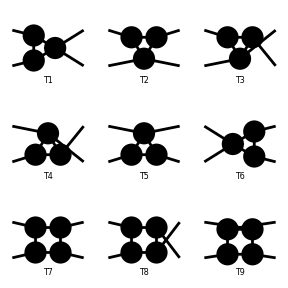

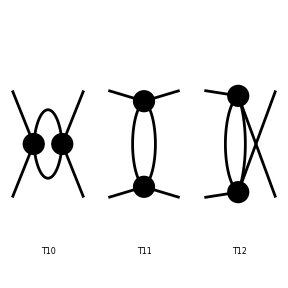

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[T2DM2S]
```

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

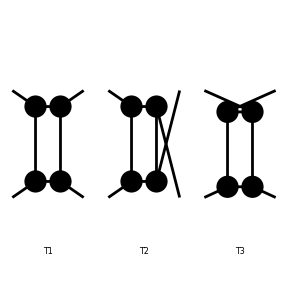

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[T2DM2S[[{7,8,9}]]]
```

Excluding 0 Generic, 6 Classes, and 14 Particles fields

inserting at level(s) {Particles}

> Top. 1: 42 Particles insertions

> Top. 2: 40 Particles insertions

> Top. 3: 42 Particles insertions

Restoring 0 Generic, 6 Classes, and 14 Particles fields

in total: 124 Particles insertions

> Top. 1: 42 diagrams

> Top. 2: 40 diagrams

> Top. 3: 42 diagrams

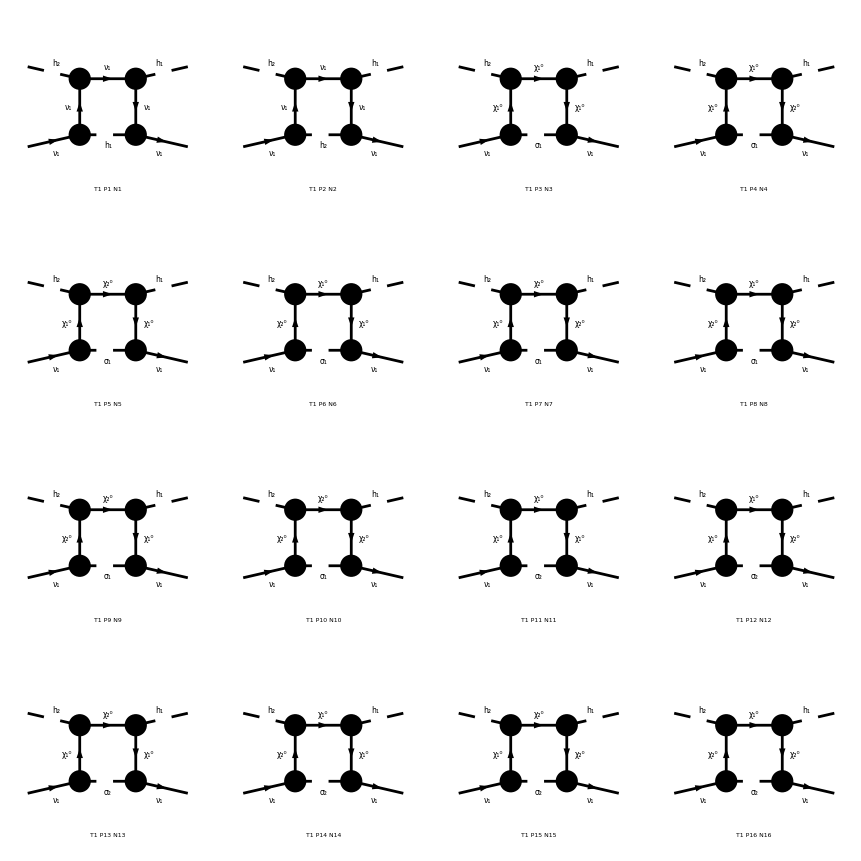

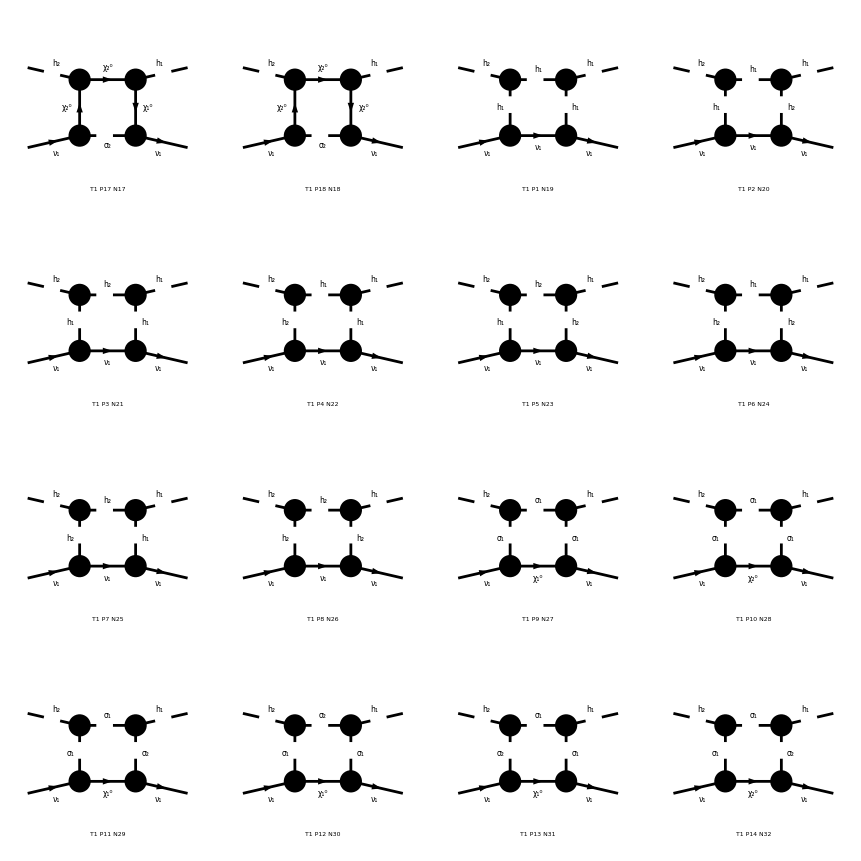

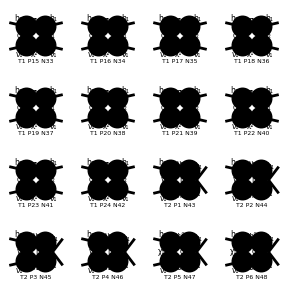

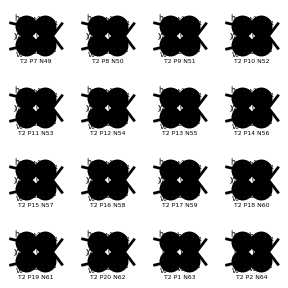

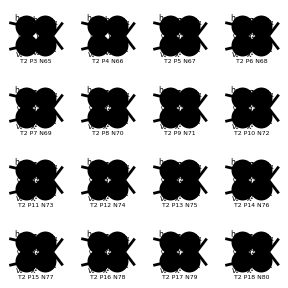

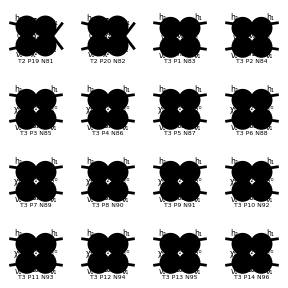

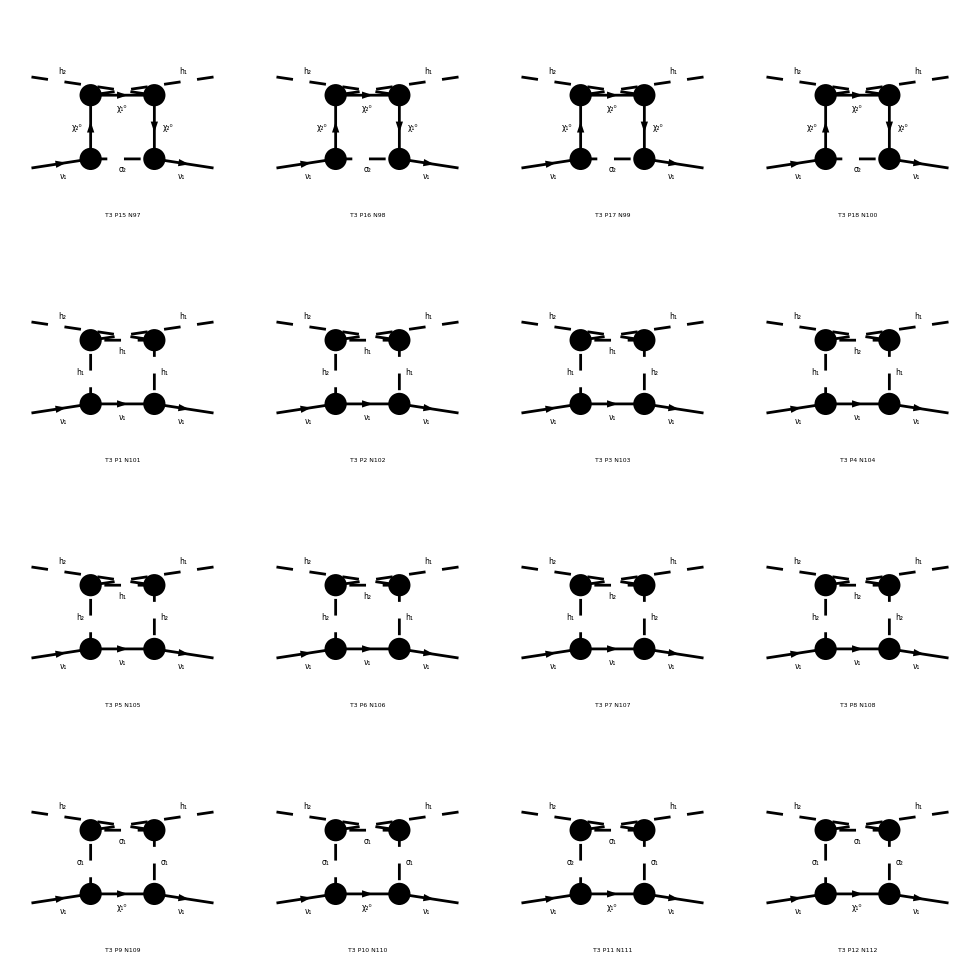

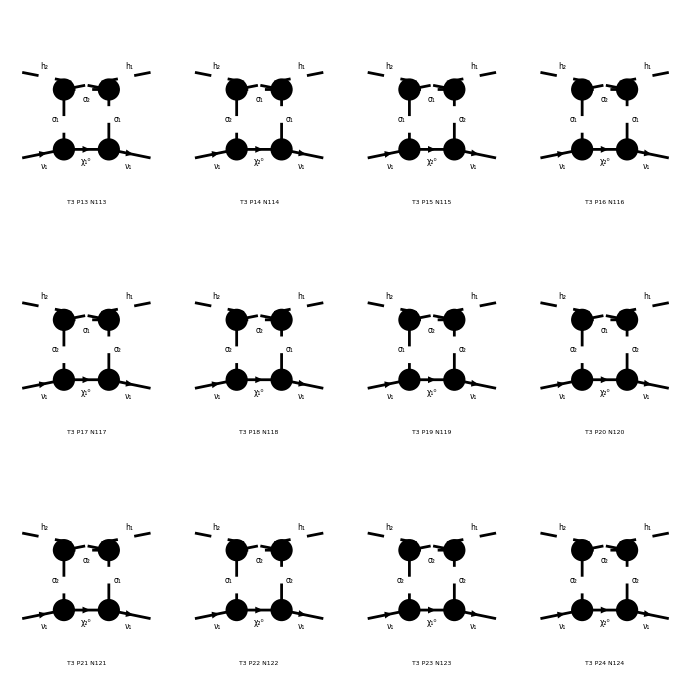

FeynArtsGraphics[{ComposedChar[h,2],ComposedChar[\nu,1]}→{ComposedChar[h,1],ComposedChar[\nu,1]}][([T1 P1 N1] | [T1 P2 N2] | [T1 P3 N3] | [T1 P4 N4]
[T1 P5 N5] | [T1 P6 N6] | [T1 P7 N7] | [T1 P8 N8]
[T1 P9 N9] | [T1 P10 N10] | [T1 P11 N11] | [T1 P12 N12]
[T1 P13 N13] | [T1 P14 N14] | [T1 P15 N15] | [T1 P16 N16]),([T1 P17 N17] | [T1 P18 N18] | [T1 P1 N19] | [T1 P2 N20]
[T1 P3 N21] | [T1 P4 N22] | [T1 P5 N23] | [T1 P6 N24]
[T1 P7 N25] | [T1 P8 N26] | [T1 P9 N27] | [T1 P10 N28]
[T1 P11 N29] | [T1 P12 N30] | [T1 P13 N31] | [T1 P14 N32]),([T1 P15 N33] | [T1 P16 N34] | [T1 P17 N35] | [T1 P18 N36]
[T1 P19 N37] | [T1 P20 N38] | [T1 P21 N39] | [T1 P22 N40]
[T1 P23 N41] | [T1 P24 N42] | [T2 P1 N43] | [T2 P2 N44]
[T2 P3 N45] | [T2 P4 N46] | [T2 P5 N47] | [T2 P6 N48]),([T2 P7 N49] | [T2 P8 N50] | [T2 P9 N51] | [T2 P10 N52]
[T2 P11 N53] | [T2 P12 N54] | [T2 P13 N55] | [T2 P14 N56]
[T2 P15 N57] | [T2 P16 N58] | [T2 P17 N59] | [T2 P18 N60]
[T2 P19 N61] | [T2 P20 N62] | [T2 P1 N63] | [T2 P2 N64]),([T2 P3 N65] | [T2 P4 N66] | [T2 P5 N67] | [T2 P6 N68]
[T2 P7 N69] | [T2 P8 N70] | [T2 P9 N71] | [T2 P10 N72]
[T2 P11 N73] | [T2 P12 N74] | [T2 P13 N75] | [T2 P14 N76]
[T2 P15 N77] | [T2 P16 N78] | [T2 P17 N79] | [T2 P18 N80]),([T2 P19 N81] | [T2 P20 N82] | [T3 P1 N83] | [T3 P2 N84]
[T3 P3 N85] | [T3 P4 N86] | [T3 P5 N87] | [T3 P6 N88]
[T3 P7 N89] | [T3 P8 N90] | [T3 P9 N91] | [T3 P10 N92]
[T3 P11 N93] | [T3 P12 N94] | [T3 P13 N95] | [T3 P14 N96]),([T3 P15 N97] | [T3 P16 N98] | [T3 P17 N99] | [T3 P18 N100]
[T3 P1 N101] | [T3 P2 N102] | [T3 P3 N103] | [T3 P4 N104]
[T3 P5 N105] | [T3 P6 N106] | [T3 P7 N107] | [T3 P8 N108]
[T3 P9 N109] | [T3 P10 N110] | [T3 P11 N111] | [T3 P12 N112]),([T3 P13 N113] | [T3 P14 N114] | [T3 P15 N115] | [T3 P16 N116]
[T3 P17 N117] | [T3 P18 N118] | [T3 P19 N119] | [T3 P20 N120]
[T3 P21 N121] | [T3 P22 N122] | [T3 P23 N123] | [T3 P24 N124]
Null | Null | Null | Null)]

```mathematica
n22=InsertFields[T2DM2S[[{7,8,9}]],{S[1,{2}],F[1,{1}]}->{S[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz",ExcludeParticles->{F[1,{2}],F[1,{3}],F[2],V[2],V[3],S[2]}];
Paint[n22,ColumnsXRows->4]
```

Amplitude in process..

```mathematica
CreateFeynAmp[n22]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{S[1],p1,Masshh,{}},{S[1],p2,Masshh,{}}}→{{S[1],k1,Masshh,{}},{S[1],k2,Masshh,{}}},Model→{SDdiracDMEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{-F[6,{2}],F[6,{2}]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],-3 Lam]]

```mathematica
resultn22=CalcFeynAmp[CreateFeynAmp[n22],FermionChains->VA,Antisymmetrize->False,Invariants->True];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 16 Particles amplitudes

> Top. 2: 16 Particles amplitudes

in total: 32 Particles amplitudes

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-14.frm

running FORM...

```mathematica
resultn22
```

resultn22

Simplifications

```mathematica
Den[x_,y_]:=1/(x-y)

expr1=Simplify[ComplexExpand[ Plus@@resultn22//.Subexpr[]//.Abbr[] //.{MassVWp->mw,MassVZ->mz,MassHp->mw,MassAh->mz, MassFe[3]->mta,MassFu[3]->mt,MassFd[3]->mb,Yu[3,3]->yt,Yd[3,3]->yb,Ye[3,3]->yta,Masshh[1]->ms1,Masshh[2]->ms2,ZH[1,1]->ZH11,ZH[1,2]->ZH12,ZH[2,1]->ZH21,ZH[2,2]->ZH22,ZX[1,1]->ZX11,ZX[1,2]->ZX12,ZX[2,1]->ZX21,ZX[2,2]->ZX22,ZX21->ZX12,ZH21->-ZH12(*,ZDL[1,1]->1,ZDL[1,2]->0,ZDL[1,3]->0,ZDR[1,1]->1,ZDR[1,2]->0,ZDR[1,3]->0*)}
]]
```

1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS ZH12 (-ms2^2 ZH11+T (ZH11-ZH22)+ms1^2 ZH22) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

Simplify: ZUL the mixing for the lef up quaks and so on... No mixing imply:

```mathematica
ZUL[a_,b_]:=KroneckerDelta[a,b];
ZUR[a_,b_]:=KroneckerDelta[a,b];
ZDL[a_,b_]:=KroneckerDelta[a,b];
ZDR[a_,b_]:=KroneckerDelta[a,b];
ZEL[a_,b_]:=KroneckerDelta[a,b];
ZER[a_,b_]:=KroneckerDelta[a,b];
```

```mathematica
expr1
```

-1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS (ms2^2 ZH11 ZH12+ms1^2 ZH1 ZH22-T (ZH11 ZH12+ZH1 ZH22)) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

#### Final Dirac Chains after de Pairs reduction

```mathematica
expr1//.{
(*,

Mat[DiracChain[Spinor[k[1],m,-1],1,Spinor[k[1],m,1]]]->0,(*cero*)
Mat[DiracChain[Spinor[k[1],m,-1],1,k[3],Spinor[k[1],m,1]]]->0,(*cero*)
Mat[DiracChain[Spinor[k[1],m,-1],1,ec[3],ec[4],k[3],Spinor[k[1],m,1]]]->FA04,
Mat[DiracChain[Spinor[k[1],m,-1],1,ec[3],ec[4],Spinor[k[1],m,1]]]->0,(*cero*)

Mat[DiracChain[Spinor[k[1],m,-1],5,Spinor[k[1],m,1]]]->FA01,
Mat[DiracChain[Spinor[k[1],m,-1],5,k[3],Spinor[k[1],m,1]]]->FA02,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[1]]]->FA05,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[3]]]->FA07,
Mat[DiracChain[Spinor[k[1],m,-1],5,Lor[1],Spinor[k[1],m,1]]*Eps[Lor[1],ec[3],ec[4],k[4]]]->FA08*)
}
```

-1/(4 √2 (ms1^2-T) (-ms2^2+T))YTS ZH12 (ms2^2 ZH11+ms1^2 ZH22-T (ZH11+ZH22)) ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]

```mathematica
Aproximation
```

```mathematica
expr2=Simplify[expr1//.{ZH11->ZH22}]
```

1/(4 √2 (ms1^2-T) (-ms2^2+T))(ms1^2-ms2^2) YTS ZH12 ZH22 ZX11 ZX12 (2 Mat[(<v1|1|u2>) (<u3|1|v4>) SUNT[Col1,Col3]]-2 Mat[(<v1|5|u2>) (<u3|5|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>) SUNT[Col1,Col3]]+2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>) SUNT[Col1,Col3]]-Mat[(<v1|1,Lor[1],Lor[2]|u2>) (<u3|1,Lor[1],Lor[2]|v4>) SUNT[Col1,Col3]]) Yd[1,1]